```mathematica
centers={};
i=1;
```

```mathematica
While[i≤ 75000,
{xtry,ytry}=1.1*{RandomReal[],RandomReal[]};
dists={};
k=1;
While[k≤ Length[centers],
dists=Append[dists,Norm[{xtry,ytry}-centers[[k]]]];
k++;];
checklist=3*ConstantArray[0.033,Length[dists]];
If[Reduce[dists≥ checklist],centers=Append[centers,{xtry,ytry}]];
i++;]
```

```mathematica
j=1;
circles={};
While[j≤ Length[centers],
circles=Append[circles,Graphics[{EdgeForm[Thickness[0.012]],RGBColor[0.5,0.5,0.5,0.3],Disk[centers[[j]],3*0.025]}]];
j++;]
```

```mathematica
q=1;
contactnetwork={};
While[q≤ Length[centers],
r=1;
While[r< q,
If[Norm[centers[[r]]-centers[[q]]]≤ 0.156,contactnetwork=Append[contactnetwork,Graphics[{Red,Thickness[0.01],Line[{centers[[r]],centers[[q]]}]}]]];
r++;];
q++;]
```

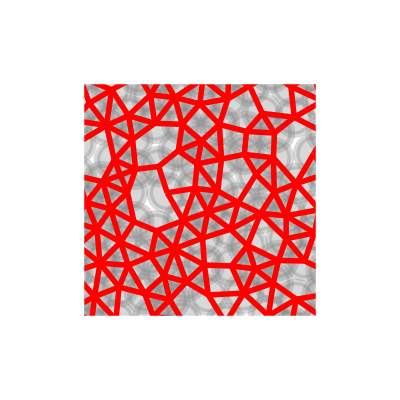

```mathematica
BorderRect=Graphics[{{White,Rectangle[{-0.156,-0.156},{0.05,1.256}]},{White,Rectangle[{1.05,-0.156},{1.256,1.256}]},{White,Rectangle[{-0.156,-0.156},{1.256,0.05}]},{White,Rectangle[{-0.156,1.05},{1.256,1.256}]}}];
Show[{circles,contactnetwork,BorderRect},AspectRatio->1]
```

```mathematica
N[(2*Length[contactnetwork])/Length[centers]]
```

4.38384

```mathematica
centers={};
i=1;
```

```mathematica
While[i≤ 75000,
{xtry,ytry}=1.1*{RandomReal[],RandomReal[]};
dists={};
k=1;
While[k≤ Length[centers],
dists=Append[dists,Norm[{xtry,ytry}-centers[[k]]]];
k++;];
checklist=3*ConstantArray[0.041,Length[dists]];
If[Reduce[dists≥ checklist],centers=Append[centers,{xtry,ytry}]];
i++;]
```

```mathematica
j=1;
circles={};
While[j≤ Length[centers],
circles=Append[circles,Graphics[{EdgeForm[Thickness[0.012]],RGBColor[0.5,0.5,0.5,0.3],Disk[centers[[j]],3*0.025]}]];
j++;]
```

```mathematica
q=1;
contactnetwork={};
While[q≤ Length[centers],
r=1;
While[r< q,
If[Norm[centers[[r]]-centers[[q]]]≤ 0.156,contactnetwork=Append[contactnetwork,Graphics[{Red,Thickness[0.01],Line[{centers[[r]],centers[[q]]}]}]]];
r++;];
q++;]
```

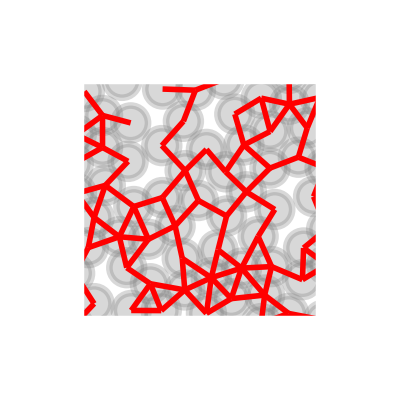

```mathematica
BorderRect=Graphics[{{White,Rectangle[{-0.156,-0.156},{0.05,1.256}]},{White,Rectangle[{1.05,-0.156},{1.256,1.256}]},{White,Rectangle[{-0.156,-0.156},{1.256,0.05}]},{White,Rectangle[{-0.156,1.05},{1.256,1.256}]}}];
Show[{circles,contactnetwork,BorderRect},AspectRatio->1]
```

```mathematica
N[(2*Length[contactnetwork])/Length[centers]]
```

2.95385